```mathematica
磁控管里电子的运动
```

```mathematica
洛伦兹力
```

```mathematica
Er=-V/(r^2 Log[r2/r1]) {x,y,0};Bz=-B0{0,0,1};
Er+{x'[t],y'[t],z'[t]}×Bz
```

```mathematica
电子运动轨迹——初速度x轴
```

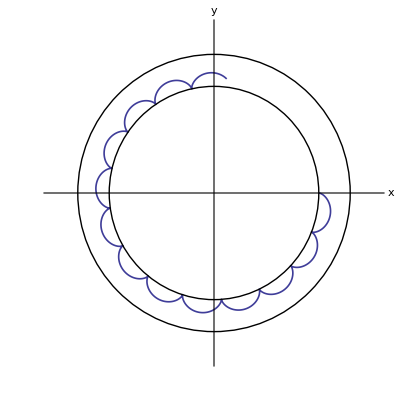

```mathematica
em=1.75851*10^11;B0=0.06;V=10^3;
r1=10^-2;r2=1.3*10^-2;tm=0.8*10^-8;
equ=
{x''[t]==
em*((V  x[t])/((x[t]^2+y[t]^2)  Log[r2/r1])+B0  y'[t]),
y''[t]==
em*((V* y[t])/((x[t]^2+y[t]^2)* Log[r2/r1])-B0  x'[t]),
x[0]==r1,x'[0]==10^6,y[0]==0,y'[0]==0};
s=NDSolve[equ,{x,y},{t,0,tm}];
{x,y}={x,y}/.s[[1]];
ParametricPlot[{x[t],y[t]},{t,0,tm},
Epilog->{Thick,Circle[{0,0},r1],
Circle[{0,0},r2]},PlotRange->1.2r2,
PlotStyle->Thickness[0.003],Ticks->None,
AspectRatio->Automatic,AxesLabel->{"x","y"}]
Clear[em,B0,V,r1,r2,equ,x,y,s]
```

```mathematica
电子运动轨迹——初速度y轴
```

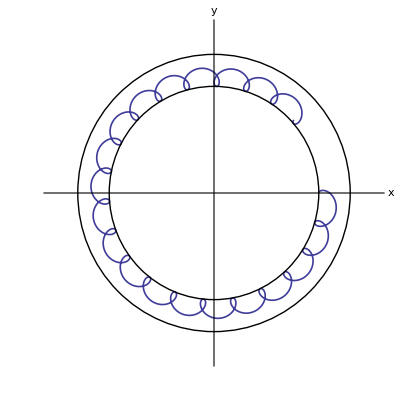

```mathematica
em=1.75851*10^11;B0=0.15;V=5*10^3;
r1=10^-2;r2=1.3*10^-2;tm=5*10^-9;
equs=
{x''[t]==
em ((V  x[t])/((x[t]^2+y[t]^2)  Log[r2/r1])+B0  y'[t]),
y''[t]==
em ((V* y[t])/((x[t]^2+y[t]^2)  Log[r2/r1])-B0 x'[t]),
x[0]==r1,x'[0]==0,y[0]==0,y'[0]==10^7};
s=NDSolve[equs,{x,y},{t,0,tm}];
{x,y}={x,y}/.s[[1]];
ParametricPlot[{x[t],y[t]},{t,0,tm},
Epilog->{Thick,Circle[{0,0},r1],
Circle[{0,0},r2]},PlotRange->1.2r2,
PlotStyle->Thickness[0.003],Ticks->None,
AspectRatio->Automatic,AxesLabel->{"x","y"}]
Clear[em,B0,V,r1,r2,equs,x,y,s]
```

```mathematica
磁控管里的洛伦茨力
```

```mathematica
Ey={0,-ξ,0};
Bx={B0,0,0};
v={x'[t],y'[t],z'[t]};
-em (Ey+v×Bx)
Clear[Ey,Bx,v]
```

{0,-em (-ξ+B0 z'[t]),B0 em y'[t]}

```mathematica
无碰撞运动
```

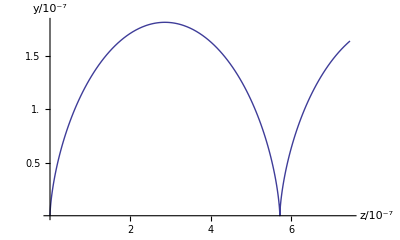

```mathematica
em=1.75851*10^11;ξ=4*10^3;B0=0.5;tm=10^-10;
equ={y''[t]==-em (-ξ+B0 z'[t]),
z''[t]==B0 em y'[t],
y[0]==0,y'[0]==0,z[0]==0,z'[0]==0};
s=NDSolve[equ,{y,z},{t,0,tm}];
ParametricPlot[({z[t],y[t]}/.s[[1]])/10^-7,
{t,0,tm},PlotPoints->200,PlotStyle->Thick,
AxesLabel->{"z/10^-7","y/10^-7"},
Ticks->{2Range[4],0.5Range[3]},
AxesStyle->Thickness[0.003],AspectRatio->0.6]
Clear[em,ξ,B0,equ,s,x,y,tm]
```

```mathematica
碰撞使轨迹升高
```

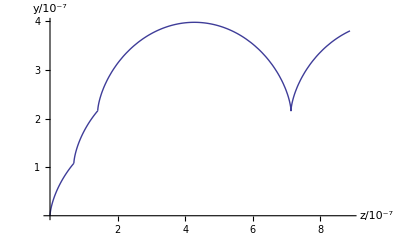

```mathematica
em=1.75851*10^11;ξ=4*10^3;B0=0.5;
t0=0.2*10^-10;tm=10^-10;
equs={y''[t]==-em (-ξ+B0 z'[t]),
z''[t]==B0 em y'[t],y[0]==y0,y'[0]==vy0,
z[0]==z0,z'[0]==vz0};
{vy0,vz0,y0,z0}={0,0,0,0};
s=NDSolve[equs,{y,z},{t,0,t0}];
{z,y}={z,y}/.s[[1]];
g1=ParametricPlot[{z[t],y[t]}/10^-7,
{t,0,t0},PlotStyle->Thick];
{y0,z0}={y[t],z[t]}/.t->t0;
Clear[y,z]
s=NDSolve[equs,{y,z},{t,0,t0}];
{z,y}={z,y}/.s[[1]];
g2=ParametricPlot[{z[t],y[t]}/10^-7,
{t,0,t0},PlotStyle->Thick];
{y0,z0}={y[t],z[t]}/.t->t0;
Clear[y,z]
s=NDSolve[equs,{y,z},{t,0,tm}];
{z,y}={z,y}/.s[[1]];
g3=ParametricPlot[{z[t],y[t]}/10^-7,
{t,0,tm},PlotStyle->Thick];
Show[{g1,g2,g3},
AxesLabel->{"z/10^-7","y/10^-7"},
Ticks->{2Range[4],Range[4]},PlotRange->All,
AxesStyle->Thickness[0.003],AspectRatio->0.6]
Clear[y,zvy0,vz0,y0,z0]
```